## Energy Function - A

```mathematica
ClearAll["Global`*"]
```

```mathematica
figPath="/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures";
export[object_,name_]:=Export[StringTemplate["``/``.pdf"][figPath,name],object,ImageResolution->1200];
```

```mathematica
Hprime[x2_,phi2_,I_,u_,v0_]:=x2^2(1-u*Cos[phi2]^2-v0/I Sin[phi2])+u*I^2*Cos[phi2]^2+2v0*I*Sin[phi2];
```

```mathematica
IConst=19/2;
A1Const=1/(2*10);
A2Const=1/(2*40);
A3Const=1/(2*20);
thetaConst=70*π/180;
jConst=11/2;
```

```mathematica
u[A1_,A3_,A_]:=(A3-A1)/A;
A[I_,j_,theta_,A1_,A2_]:=A2(1-j*Sin[theta]/I)-A1;
v0[j_,theta_,A1_,A_]:=(-A1*j*Cos[theta])/A;
```

```mathematica
AConst=A[IConst,jConst,thetaConst,A1Const,A2Const];
uConst=u[A1Const,A3Const,AConst];
v0Const=v0[jConst,thetaConst,A1Const,AConst];
HprimeMin=N[-2*v0Const*IConst];
```

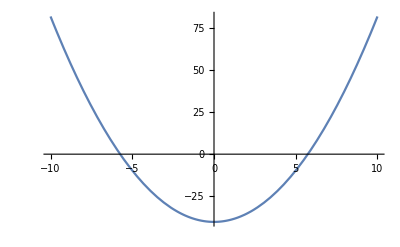

```mathematica
p1=Plot[{Hprime[x,-π/2,IConst,uConst,v0Const]},{x,-10,10}];
Show[p1]
export[p1,"Energy-Function-New-Boson-A1-phi2-const"];
```

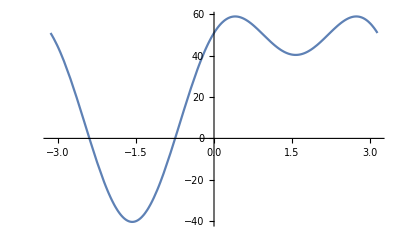

```mathematica
p2=Plot[{Hprime[0,x,IConst,uConst,v0Const]},{x,-π,π}];
Show[p2]
export[p2,"Energy-Function-New-Boson-A1-x2-const"];
```